# Motion of a classical particle in a box

Free classical particle moving around in a box

## We will make an animated picture of our particle moving around inside a box before collision with the walls

The first step is to create a box and a point with given coordinates withing the box

Make a Raster:

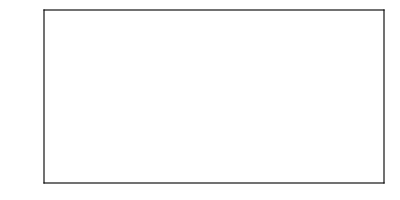

```mathematica
mybox[mx_Integer,ny_Integer]:=Graphics[Raster[ConstantArray[1,{ny,mx}]],Frame->True,FrameTicks->None];
mybox[20,10]
```

Make a Raster with a dot:

```mathematica
mybox[{mx_Integer,ny_Integer},{px_Integer,qy_Integer}]:=Graphics[Raster[ReplacePart[ConstantArray[{1,1,1},{ny,mx}],{qy,px}->{1,0,0}]],Frame->True,FrameTicks->None];
mybox[{20,10},{5,5}]
```

-Graphics-

Make a simple animation of this before collisions with a wall:

```mathematica
Animate[mybox[{20,10},{u,v}],{u,5,8,1},{v,5,8,1}]
```

Build the above into a single function:

```mathematica
myAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{u,v}],{u,x0,mx,vx},{v,y0,ny,vy}];
myAnimatedbox[{20,10},{5,5},{1,1}]
```

Make the animated box more uniform using a single parameter (time):

```mathematica
mytimeAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{x0 + vx t,y0 + vy t}],{t,0,Min[(mx-x0)/vx,(ny-y0)/vy],1}];
```

```mathematica
mytimeAnimatedbox[{20,10},{5,5},{1,1}]
```

## What happens after collision with a wall?

We can treat the x and y directions independently (need one function for both directions)

What happens after the n^th time step in one direction? The function that defines the position is:

```mathematica
f[c_Integer,v_Integer,cmax_Integer,t_Integer]:=1+If[EvenQ[Floor[(c+v (t-1))/(cmax-1)]],Mod[c + v (t-1),cmax-1],(cmax-1)Floor[(c+v (t-1))/(cmax-1)+1]-c-v (t-1)];
```

After the n^th time step the x-position looks like:

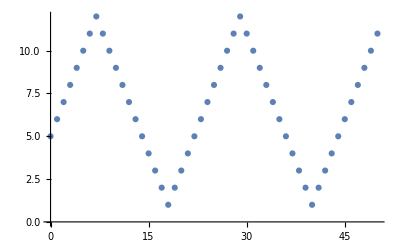

```mathematica
ListPlot[Table[{n,f[5,1,12,n]},{n,0,50}]]
```

Implement this in the animated box (both x and y directions):

```mathematica
myimprovedtimeAnimatedbox[{mx_Integer,ny_Integer},{x0_Integer,y0_Integer},{vx_Integer,vy_Integer}]:=Animate[mybox[{mx,ny},{f[x0,vx,mx,t],f[y0,vy,ny,t]}],{t,0,Min[(mx-x0)/vx,(ny-y0)/vy],1}];
```

Same as previous answer since time restriction still present:

```mathematica
myimprovedtimeAnimatedbox[{20,10},{5,5},{1,1}]
```

Lift the time limitations on the animation:

```mathematica
myFinalbox[{m_Integer,n_Integer},{x_Integer,y_Integer},{vx_Integer,vy_Integer},tt_Integer]:=Animate[mybox[{m,n},{f[x,vx,m,t],f[y,vy,n,t]}],{t,0,tt,1}];
```

```mathematica
myFinalbox[{60,40},{35,5},{1,1},600]
```

Let us slow down the animation for better visual effects:

```mathematica
myFinalAnimatedbox[{m_Integer,n_Integer},{x_Integer,y_Integer},{vx_Integer,vy_Integer},tt_Integer]:=Animate[mybox[{m,n},{f[x,vx,m,t],f[y,vy,n,t]}],{t,0,tt,1},AnimationRate->20,AnimationRunning->True];
```

```mathematica
myFinalAnimatedbox[{60,40},{35,5},{1,1},600]
```

## Examples of the final animated graphics

Here is an example of an animated final result:

Size of this box:  60 x 40
Initial conditions:  Position ->  30, 5;  Velocity -> 1,1;  Total number of time steps -> 600;

```mathematica
myFinalAnimatedbox[{60,40},{30,5},{1,1},600]
```

Authorship information

Bhubanjyoti Bhattacharya

June 20, 2017

bhujyo@gmail.com